# Въведение в Wolfram Mathematica

## Основни операции

```mathematica
2+3
3.5-2.8
2*4
10/2
12^3
2x+3x
5!
Sqrt[121]
Sin[Pi]
ArcTan[1]
```

5

0.7

8

5

1728

5 x

120

11

0

π/4

## Скобите в Mathematica

## Кръгли скоби

```mathematica
x (x+2)^2
(x+y(1-y))^2
```

x (2+x)^2

(x+(1-y) y)^2

## Квадратни скоби - заграждат аргументите на даден оператор

```mathematica
Sqrt[60+4]
ArcSin[Sin[Pi/2]]
Log[E]
```

## Фигурни скоби - заграждат елементите на списък

```mathematica
{1,2,3,4}
```

## Mathematica не може да разбере какво имаме предвид със следните изрази:

```mathematica
[x+y(1-y)]^2  
(* (x+y(1-y))^2 *)
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
(1,2)
(* {1,2} *)
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Sin(Pi)
(* Sin[Pi] *)
```

π Sin

## Символно и числено пресмятане

### Обикновено Mathematica смята символно (и следователно точно), ако не сме указали друго

```mathematica
123/Sqrt[768]
Cos[Pi/12]
Log[2]
```

### Можем да смятаме числено по следния начин:

```mathematica
N[123/Sqrt[768]]
N[Cos[Pi/12]]
N[Log[2]]
```

```mathematica
123./Sqrt[768]
Cos[Pi/12.]
Log[2.0]
```

## Графики

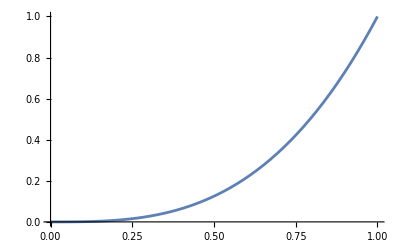

```mathematica
Plot[x^3, {x,0,1}]
```

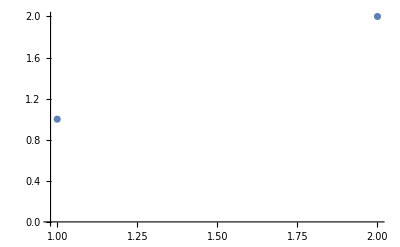

```mathematica
ListPlot[{{1,1},{2,2}}]
```

### Дефиниране на функции

```mathematica
p[x_]:=x^2+5
g[x_]=Log[5.0*x];
p[5]
g[1]
```

30

1.60944

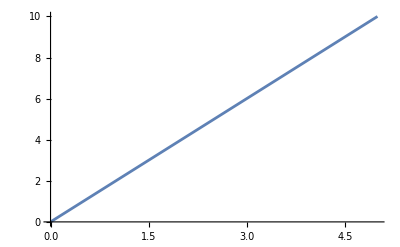

D::ivar: 0.000102143 is not a valid variable.

D::ivar: 0.102143 is not a valid variable.

D::ivar: 0.204184 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
p[x_]=D[x^2,x];
Plot[p[x],{x,0,5}]

p[x_]:=D[x^2,x]
Plot[p[x],{x,0,5}] (*не работи тъй като сме сложили : в дефиницията на p[x]*)
```

# Популационна динамика

Намерете подходящ модел, който описва данните :

```mathematica
{{брой дни, 0, 2, 4, 6, 8, 10, 12, 14}, {бр. Paramecium 
aurelia (в капка), 4, 10, 46, 66, 70, 69, 71, 71}}
```

{{дни брой,0,2,4,6,8,10,12,14},{в капка aurelia бр.Paramecium,4,10,46,66,70,69,71,71}}

Малтус (r=0.55)

```mathematica
(*намиране на точното решение*)
uExact[t_] = 
 DSolve[{u'[t] == 0.55 u[t], u[0] == 4}, u[t], t][[1, 1, 2]]
```

4. ⅇ^(0.55 t)

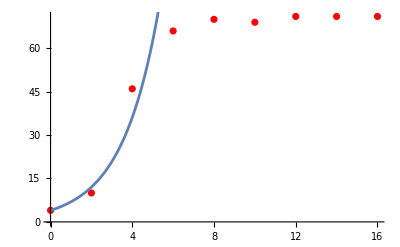

```mathematica
plot1 = ListPlot[{{0, 4}, {2, 10}, {4, 46}, {6, 66}, {8, 70}, {10, 
     69}, {12, 71}, {14, 71}, {16, 71}}, PlotStyle -> Red];
plot2 = Plot[uExact[t], {t, 0, 16}];
Show[plot1, plot2]
```

Ферхълст (r=0.012)

```mathematica
uExact[t_] = 
 DSolve[{u'[t] == 0.012 u[t] (71 - u[t]), u[0] == 4}, u[t], t][[1, 1, 
  2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(71. 2.71828^(0.852 t))/(16.75+2.71828^(0.852 t))

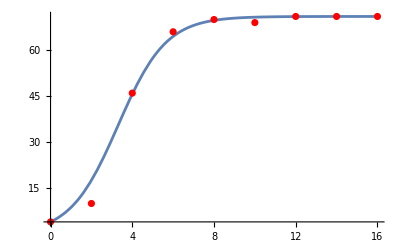

```mathematica
plot3 = Plot[(71*4*E^(71*0.012*t))/(71 + 4*(E^(71*0.012*t) - 1)), {t, 
    0, 16}, PlotRange -> All];
Show[plot3, plot1]
```

# Приближаване на производна на функция

## Визуализация

```mathematica
PlotDer[f_, x1_, start_, end_] :=
 (
  minF = Min[Table[f[x], {x, start, end, 0.1}]] - 1;
  maxF = Max[Table[f[x], {x, start, end, 0.1}]] + 1;
  Manipulate[
   	Show[
                                         Plot[{f[x], Limit[(f[x1] - f[y])/(x1 - y), y -> x2]*(x - x2) + f[x2]}, {x, start, end}, PlotRange -> {{start, end}, {minF, maxF}}],
    		Plot[{Limit[(f[x1] - f[y])/(x1 - y), y -> x1]*(x - x1) + f[x1]}, {x, start, end},  PlotRange -> {{start, end}, {minF, maxF}}, PlotStyle -> Black],
    		ParametricPlot[{x, If[Abs[f[x1]] > Abs[f[x2]], f[x2], f[x1]]}, {x, Min[0, x1, x2], Max[0, x1, x2]}, PlotStyle -> {Gray, Dashed}],
    		ParametricPlot[{x, Max[f[x1], f[x2]]}, {x, 0, If[f[x1] > f[x2], x1, x2]}, PlotStyle -> {Gray, Dashed}],
    		ParametricPlot[{x1, x}, {x, 0, f[x1]}, PlotStyle -> {Gray, Dashed}],
    		ParametricPlot[{x2, x}, {x, 0, f[x2]}, PlotStyle -> {Gray, Dashed}],
    		ListPlot[{{x1, f[x1]}, {x2, f[x2]}}, PlotStyle -> Orange]
    	], {x2, start, end, 0.01}]
  )

p[x_] := Exp[x]
PlotDer[p, 0.1, 0, 2]
```

## Приближете на производна на e^x в интервала [0,3], като използвате

### формулата с разлика напред

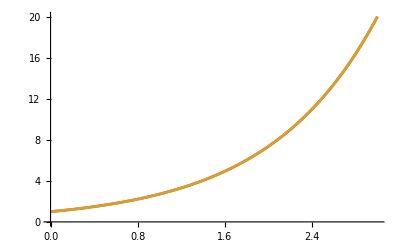

```mathematica
Δt = 0.001;
f[x_] = Exp[x];
DerF[x_] = D[f[x], x];
Plot[{DerF[x], (f[x + Δt] - f[x])/Δt}, {x, 0, 3}]
```